Задание переменных и функций:
x=1; F[x_]:=x^2;
Применение функции:
	 F@x                        (⇔F[x])
		x//F                    (⇔F[x])
		F@@{x,y,z}   (⇔F[x,y,z])
		F/@{x,y,z}   (⇔{F[x],F[y],F[z]})
Анонимные функции:
	#^2&     (⇔F[x_]:=x^2)

# Графики

```mathematica
tab=100Sin/@Range[7]
```

{100 Sin[1],100 Sin[2],100 Sin[3],100 Sin[4],100 Sin[5],100 Sin[6],100 Sin[7]}

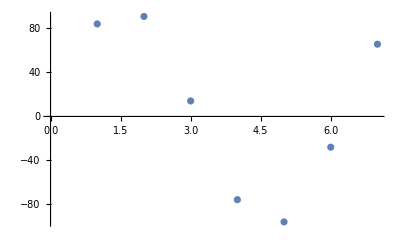

```mathematica
ListPlot[tab]
```

```mathematica
xs=10Range[7]
```

{10,20,30,40,50,60,70}

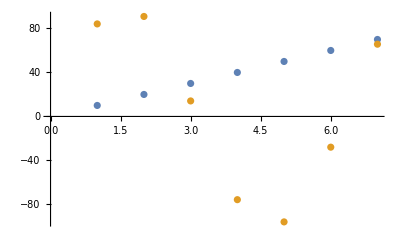

```mathematica
ListPlot[{xs,tab}]
```

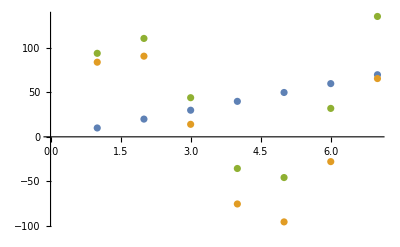

```mathematica
ListPlot[{xs,tab,xs+tab}]
```

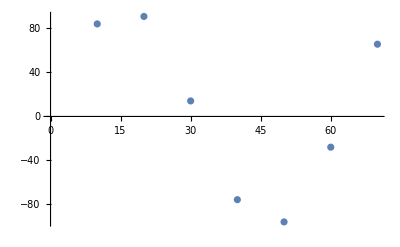

```mathematica
ListPlot[{xs,tab}ᵀ]
```

```mathematica
{xs,tab}
{xs,tab}ᵀ
```

{{10,20,30,40,50,60,70},{100 Sin[1],100 Sin[2],100 Sin[3],100 Sin[4],100 Sin[5],100 Sin[6],100 Sin[7]}}

{{10,100 Sin[1]},{20,100 Sin[2]},{30,100 Sin[3]},{40,100 Sin[4]},{50,100 Sin[5]},{60,100 Sin[6]},{70,100 Sin[7]}}

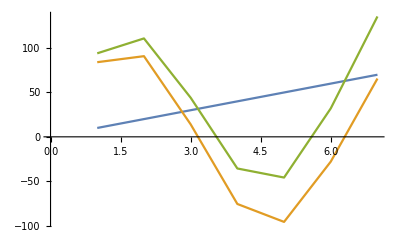

```mathematica
ListLinePlot[{xs,tab,xs+tab}]
```

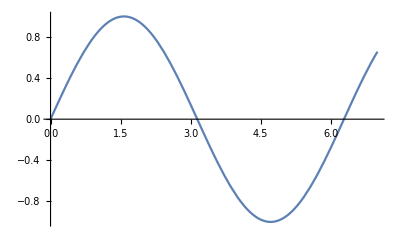

```mathematica
Plot[Sin[x],{x,0,7}]
```

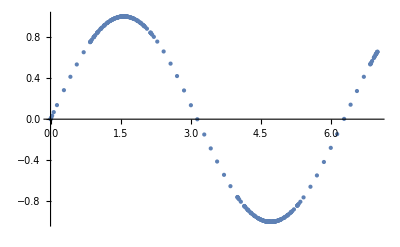

```mathematica
Plot[Sin[x],{x,0,7}]/.Line->Point
```

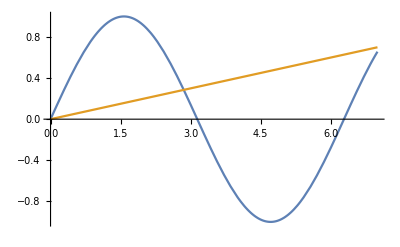

```mathematica
Plot[{Sin[x],x/10},{x,0,7}]
```

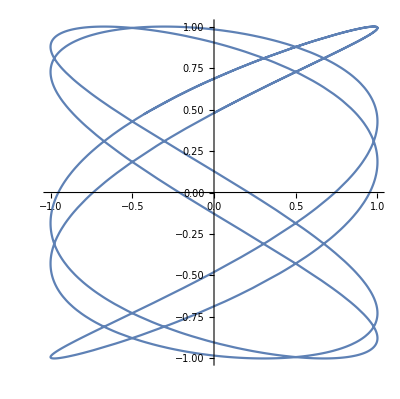

```mathematica
ParametricPlot[{Sin[5 t],Sin[3t+.5]},{t,0,7}]
```

Plot[]
ListPlot[]
ParametricPlot[]
ContourPlot[]
LogLogPlot[]
PolarPlot[]
…
Plot3D[]
…

```mathematica
%4
```

{10 Sin[1],10 Sin[2],10 Sin[3],10 Sin[4],10 Sin[5],10 Sin[6],10 Sin[7]}

# Задача

```mathematica
x0=0;y0=0;v0x=1;v0y=.3;
Animate[
ParametricPlot[{TriangleWave[x0+v0x t],TriangleWave[y0+v0y t]},{t,0,T},PlotRange->{{-1,1},{-1,1}}]
,{T,1,10}]
```